```mathematica
Clear[alphaMas, alphaMenos, alphaZ, Ω, β]
```

```mathematica
β = 0.1; Ω = 0.1;
```

#### Lineal

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + I Ω(1 + x[t]^2)== 0 ,y'[t] == I(Ω x[t] - (β^2 )t),z'[t]Exp[-2 y[t]]+ I Ω == 0, x[-150]==y[-150]==z[-150]== 0},{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

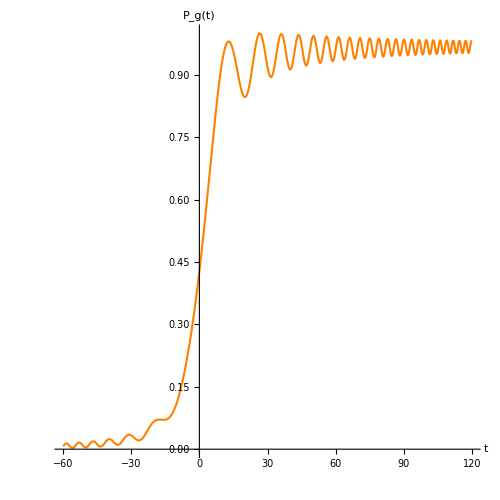

```mathematica
P1 = Plot[(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], {t, -60, 120}, 
PlotLegends-> "Lineal P_(g → e)",AxesLabel-> {Style["t",16,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_g(t)",16,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500, PlotStyle->{Thickness[0.003], Orange}]
```

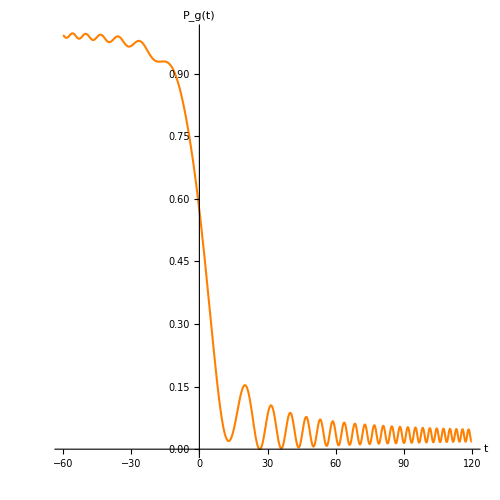

```mathematica
P2 = Plot[Abs[Exp[- alphaZ[t]] ]^2, {t, -60, 120}, PlotLegends-> "Lineal P_(g → g)",AxesLabel-> {Style["t",14,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_g(t)",14,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500, PlotStyle->{Thickness[0.003], Orange}]
```

#### Hiperbolico

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + I Ω(1 + x[t]^2)== 0 ,y'[t] == I(Ω x[t] - Tanh[(β t)/2]),z'[t]Exp[-2 y[t]]+ I Ω == 0, x[-150]==y[-150]==z[-150]== 0},{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

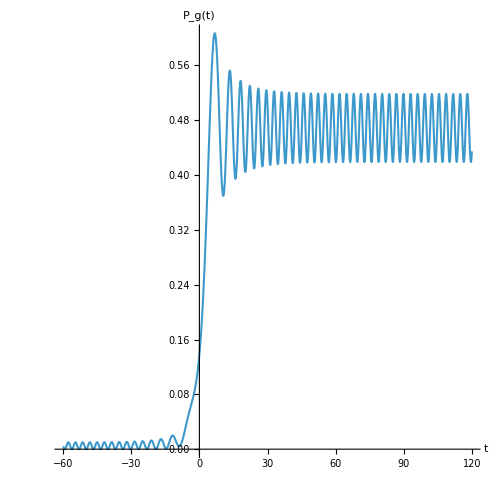

```mathematica
P3=Plot[(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], {t, -60, 120},PlotLegends-> "Hiperbolico P_(g → e)",AxesLabel-> {Style["t",14,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_g(t)",14,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500, PlotStyle->Thickness[0.003]]
```

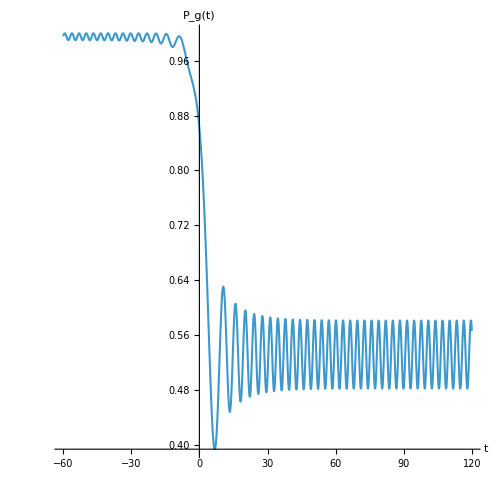

```mathematica
P4=Plot[Abs[Exp[- alphaZ[t]] ]^2, {t, -60, 120},  PlotLegends-> "Hiperbolico P_(g → g)",AxesLabel-> {Style["t",14,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_g(t)",14,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500, PlotStyle->Thickness[0.003]]
```

### Comparación

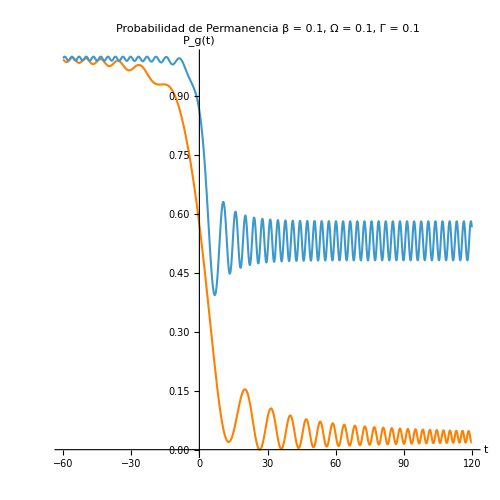

```mathematica
Show[P2,P4,
PlotLabel->Style["Probabilidad de Permanencia \n β = 0.1, Ω = 0.1, Γ = 0.1\n", 16, FontFamily->"Times New Roman", Black]
]
```